# A package for Carlson integrals

J. M., version of 03/2019

## Introduction

Carlson is a Mathematica package that implements the symmetric elliptic integrals of B. C. Carlson. These functions are intended to replace the standard Legendre-Jacobi elliptic integrals (EllipticF, EllipticE, EllipticPi in Mathematica).

Load the package:

```mathematica
<<Carlson`
```

These are the Carlson functions implemented:

```mathematica
??Carlson`*
```

## Basic Examples

Circumference of an ellipse:

```mathematica
With[{a=√2,b=1},
N[{2π CarlsonRE[a^2,b^2],ArcLength[{a Cos[t],b Sin[t]},{t,0,2π}]},20]]
```

{7.6403955780554240358,7.6403955780554240358}

Surface area of an ellipsoid:

```mathematica
With[{a=3,b=2,c=1},
N[{4π a b c CarlsonRG[1/a^2,1/b^2,1/c^2],RegionMeasure[RegionBoundary[Ellipsoid[{0,0,0},{a,b,c}]]]},20]]
```

{48.882146302582059696,48.882146302582059696}

Total arc length of a lemniscate of Bernoulli:

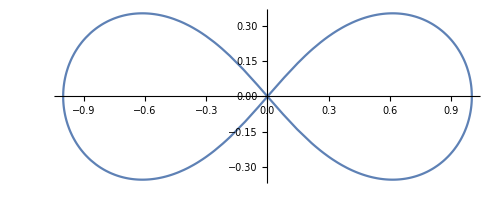

```mathematica
ParametricPlot[{Cos[t]/(1+Sin[t]^2),(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π}]
```

```mathematica
N[{2π CarlsonRK[1,2],ArcLength[{Cos[t]/(1+Sin[t]^2),(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π}]},20]
```

{5.2441151085842396209,5.2441151085842396209}

Evaluate a singular value:

```mathematica
N[{{π CarlsonRK[4,(8+3 √7)/4],(Gamma[1/7]Gamma[2/7]Gamma[4/7])/(4 7^(1/4)π)},
{π CarlsonRE[1/4,(8+3 √7)/64],π^2/(7^(1/4) Gamma[1/7] Gamma[2/7] Gamma[4/7])+((2+√7) Gamma[1/7] Gamma[2/7] Gamma[4/7])/(8 7^(3/4) π)}},20]
```

{{1.5723397534061375274,1.5723397534061375274},{1.5692551723793890516,1.5692551723793890516}}

A parametrization of a Mylar balloon (two flat sheets of plastic sewn together at their circumference and then inflated):

```mathematica
With[{kk=N[π CarlsonRK[2,4]]},
ParametricPlot3D[{JacobiCN[u,1/2]Cos[v],JacobiCN[u,1/2]Sin[v],
1/(√2)(JacobiSN[u,1/2]CarlsonRF[JacobiCN[u,1/2]^2,JacobiDN[u,1/2]^2,1]-1/3 JacobiSN[u,1/2]^3 CarlsonRD[JacobiCN[u,1/2]^2,JacobiDN[u,1/2]^2,1])},
{u,-kk,kk},{v,-π,π},PlotRange->All]]
```

-Graphics3D-

Solid angle subtended by a circular disk:

```mathematica
With[{L=2,r0=2/5,rm=1},
Graphics3D[{EdgeForm[],Polygon[PadRight[N@CirclePoints[rm,24],{Automatic,3}]],{Dashed,Line[{{r0,0,0},{r0,0,L}}]},Sphere[{r0,0,L},rm/20]},Boxed->False,ViewPoint->{-2.4,-1.3,2.}]]
```

-Graphics3D-

```mathematica
With[{L=2,r0=2/5,rm=1},
N[2π Boole[r0<rm]+2π L rm(r0 (r0-rm)(L^2+(r0+rm)^2)CarlsonRM[(L^2+(r0-rm)^2)(r0+rm)^2,(L^2+(r0+rm)^2)(r0+rm)^2,(L^2+(r0+rm)^2)(r0-rm)^2]-CarlsonRK[(L^2+(r0-rm)^2)(r0+rm)^2,(L^2+(r0+rm)^2)(r0+rm)^2]),20]]
```

0.63704888834757616694

```mathematica
With[{L=2,r0=2/5,rm=1},
L NIntegrate[r/((r^2-2r0 r Cos[θ]+r0^2+L^2)^(3/2)),{r,0,rm},{θ,0,2π},WorkingPrecision->20]]
```

0.63704888834775923209

Distance along Earth’s meridian:

```mathematica
With[{a=UnitConvert[GeodesyData["ITRF00","SemimajorAxis"],"Kilometers"],e=GeodesyData["ITRF00","Eccentricity"],φ=26°},
a(1-e^2)(Sin[φ]CarlsonRF[Cos[φ]^2,1-e^2 Sin[φ]^2,1]+e^2/3 Sin[φ]^3 CarlsonRD[Cos[φ]^2,1-e^2 Sin[φ]^2,1])]
```

2876.83 km

```mathematica
GeoDistance[GeoPosition[{0,0}],GeoPosition[{26,0}]]
```

2876.83 km

Volume of cylinder-ball intersection:

```mathematica
With[{R=1/6,r=5/9,b=5/11},
Graphics3D[{Cylinder[{{0,0,0},{0,0,2r}},R],Ball[{b,0,r},r]}]]
```

-Graphics3D-

```mathematica
With[{R=1/6,r=5/9,b=5/11},
N[(2π)/9(2R(3 R (2 r^2-R^2)-b (b^2-4 r^2+5 b R+7 R^2)+(3 r^4)/(b-R))CarlsonRK[(b-r+R) (b+r+R),4b R]+
(b^2-4 r^2+7 R^2)CarlsonRE[(b-r+R) (b+r+R),4b R]+
6b R r^4(b+r-R) (b+R) (b-r-R)CarlsonRM[(b-R)^2 (b-r+R) (b+r+R),4 b R(b-R)^2,4 b R r^2]),20]]
```

0.046369746842429356396

```mathematica
With[{R=1/6,r=5/9,b=5/11},
Volume[RegionIntersection[Cylinder[{{0,0,0},{0,0,2r}},R],Ball[{b,0,r},r]],Method->{"NIntegrate",WorkingPrecision->20}]]
```

0.046369746842430010527

Expectation value of the square root of a quadratic form, relative to a normal distribution:

```mathematica
MatrixForm[mat=HilbertMatrix[3]]
```

(1 | 1/2 | 1/3
1/2 | 1/3 | 1/4
1/3 | 1/4 | 1/5)

```mathematica
N[Gamma[(1+3)/2]/Gamma[3/2](CarlsonRG@@Eigenvalues[mat]),25]
```

0.7339307225283869601322272

```mathematica
NExpectation[√({u,v,w}.mat.{u,v,w}),{u,v,w}\[Distributed]MultinormalDistribution[{0,0,0},IdentityMatrix[3]/2],WorkingPrecision->25]//Quiet
```

0.7339307151694690435391797

Express the elliptic logarithm in terms of Carlson functions:

```mathematica
With[{x=1,a=2,b=6},
N[{-CarlsonRF[x,x+(a+√(a^2-4b))/2,x+(2b)/(a+√(a^2-4b))],EllipticLog[{x,√(x^3+a x^2+b x)},{a,b}]},25]//Chop]
```

{-0.7098518800801157325978,-0.7098518800801157325978}

## Available Functions

Details on the functions implemented in the package can be found in the following sections.

### CarlsonRC

```mathematica
??CarlsonRC
```

CarlsonRC[x,y] gives the Carlson elementary integral R_C(x,y).

CarlsonRC[x,y] is defined as the value of the integral 1/2∫_0^∞ (t+x)^(-1/2)(t+y)^-1 dt, for x not a negative number and nonzero y, and the Cauchy principal value is taken if y is negative.

Evaluation as a degenerate elliptic integral:

```mathematica
CarlsonRF[x,y,y]
```

CarlsonRC[x,y]

Expression as an integral over a line segment:

```mathematica
With[{x=1+2ⅈ,y=3+4ⅈ},
{N[CarlsonRC[x,y],20],NIntegrate[1/(√(x t^2+y(1-t^2))),{t,0,1},WorkingPrecision->20]}]
```

{0.44581534402500237581-0.2362936735300031118 ⅈ,0.44581534402500237582-0.2362936735300031118 ⅈ}

The Schwab-Borchardt identity:

```mathematica
With[{x=3,y=5},
N[{CarlsonRC[x,y],CarlsonRC[((√x+√y)/2)^2,(√x+√y)/2 √y]},20]]
```

{0.48416959165156247912,0.48416959165156247912}

An elementary evaluation:

```mathematica
With[{x=2,y=-3},
N[{CarlsonRC[x,y],1/(√(x-y))Log[(√x+√(x-y))/(√-y)]},20]]
```

{0.33339691011136726707,0.33339691011136726707}

Evaluate two-argument arctangent:

```mathematica
With[{x=2,y=-3},
N[{2y CarlsonRC[(x+√(x^2+y^2))^2,2 √(x^2+y^2)(x+√(x^2+y^2) )],ArcTan[x,y]},20]]
```

{-0.98279372324732906799,-0.98279372324732906799}

### CarlsonRK

```mathematica
??CarlsonRK
```

CarlsonRK[x,y] gives the complete Carlson integral of the first kind R_K(x,y).

CarlsonRK[x,y] is defined as  R_K(x,y)=2/π R_F(0,x,y), for x,y not a negative number.  It is symmetric in all of its arguments.

Evaluation as a complete elliptic integral:

```mathematica
2/π CarlsonRF[0,x,y]
```

CarlsonRK[x,y]

Imaginary modulus transformation:

```mathematica
With[{m=-1},
CarlsonRK[1,1-m]==1/(√(1-m))CarlsonRK[1,1-m/(m-1)]//N]
```

True

Relationship with the arithmetic-geometric mean:

```mathematica
With[{x=1+2ⅈ,y=3+4ⅈ},
N[{CarlsonRK[x,y],1/ArithmeticGeometricMean[√x,√y]},20]]
```

{0.47427381575433505042-0.2616423052882962921 ⅈ,0.47427381575433505042-0.2616423052882962921 ⅈ}

Elliptic nome in terms of Carlson integrals:

```mathematica
With[{m=3/4},
N[{EllipticNomeQ[m],Exp[-π CarlsonRK[1,m]/CarlsonRK[1,1-m]]},20]]
```

{0.085795733702194766517,0.085795733702194766517}

Partial differential equation satisfied by the function:

```mathematica
{x,y}.Grad[CarlsonRK[x,y],{x,y}]==-1/2 CarlsonRK[x,y]//Simplify
```

True

### CarlsonRE

```mathematica
??CarlsonRE
```

CarlsonRE[x,y] gives the complete Carlson integral of the second kind R_E(x,y).

CarlsonRE[x,y] is defined as  R_E(x,y)=4/π R_G(0,x,y), for x,y not a negative number.  It is symmetric in all of its arguments.

Evaluation as a complete elliptic integral:

```mathematica
4/π CarlsonRG[0,x,y]
```

CarlsonRE[x,y]

Imaginary modulus transformation:

```mathematica
With[{m=-1},
CarlsonRE[1,1-m]==√(1-m)CarlsonRE[1,1-m/(m-1)]//N]
```

True

Relationship with the arithmetic-geometric mean:

```mathematica
With[{x=1+2ⅈ,y=3+4ⅈ},
N[{CarlsonRE[x,y],2/π (√x+√y) EllipticE[((√x-√y)/(√x+√y))^2]-(√x √y)/ArithmeticGeometricMean[√x,√y]},20]]
```

{1.6553112236971961633+0.8944418982740955529 ⅈ,1.6553112236971961633+0.8944418982740955529 ⅈ}

Legendre’s relation:

```mathematica
With[{x=2,y=3},
N[CarlsonRE[y-x,y]CarlsonRK[x,y]+CarlsonRE[x,y]CarlsonRK[y-x,y]-y CarlsonRK[x,y]CarlsonRK[y-x,y]==2/π]]
```

True

Partial differential equation satisfied by the function:

```mathematica
{x,y}.Grad[CarlsonRE[x,y],{x,y}]==1/2 CarlsonRE[x,y]//Simplify
```

True

### CarlsonRM

```mathematica
??CarlsonRM
```

CarlsonRM[x,y,p] gives the complete Carlson integral of the third kind R_M(x,y,p).

CarlsonRM[x,y,p] is defined as  R_M(x,y,p)=4/(3π)R_J(0,x,y,p), for x,y not a negative number, and the Cauchy principal value is taken if p is negative. It is symmetric in x and y.

Evaluation as a complete elliptic integral:

```mathematica
4/(3π)CarlsonRJ[0,x,y,p]
```

CarlsonRM[x,y,p]

Expression as an Appell hypergeometric function:

```mathematica
With[{x=1,y=4,p=7},
N[{CarlsonRM[x,y,p],1/p^(3/2)AppellF1[3/2,1/2,1/2,2,1-x/p,1-y/p]},20]]
```

{0.12741061210680872199,0.12741061210680872199}

Jacobi zeta function in terms of Carlson integrals:

```mathematica
With[{ϕ=2π/5,m=1/3},
N[{JacobiZeta[ϕ,m],m/4 Sin[2ϕ] √(1-m Sin[ϕ]^2)CarlsonRM[1-m,1,1-m Sin[ϕ]^2]/CarlsonRK[1-m,1]},20]]
```

{0.056324800831035135628,0.056324800831035135628}

Evaluation in terms of other Carlson integrals:

```mathematica
With[{x=1,y=4,p=7},
N[{CarlsonRM[x,y,p],2/(√(p (p-x)))((y CarlsonRK[x,y]-CarlsonRE[x,y])CarlsonRF[y(p-x),p(y-x),y(y-x)]+(y(y-x) (p-y))/3 CarlsonRK[x,y]CarlsonRD[y(p-x),p(y-x),y(y-x)])},20]]
```

{0.12741061210680872199,0.12741061210680872199}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{n=1/5,m=2/3},
N[{EllipticPi[n,m],π/2 CarlsonRK[1-m,1]+(n π)/4 CarlsonRM[1-m,1,1-n]},20]]
```

{2.3030227051235396357,2.3030227051235396357}

### CarlsonRL

```mathematica
??CarlsonRL
```

CarlsonRL[x,y,p] gives the alternate complete Carlson integral of the third kind R_L(x,y,p).

CarlsonRL[x,y,p] is defined as  R_L(x,y,p)=8/(3π)R_H(0,x,y,p), for x,y not a negative number, and the Cauchy principal value is taken if p is negative. It is symmetric in x and y.

Evaluation as a complete elliptic integral:

```mathematica
8/(3π)CarlsonRH[0,x,y,p]
```

CarlsonRL[x,y,p]

Expression as an Appell hypergeometric function:

```mathematica
With[{x=1,y=4,p=7},
N[{CarlsonRL[x,y,p],1/(√p)AppellF1[1/2,1/2,1/2,2,1-x/p,1-y/p]},20]]
```

{0.48100621587068911076,0.48100621587068911076}

Relationship between the two complete Carlson integrals of the third kind:

```mathematica
With[{x=3,y=5,p=-1},
N[{CarlsonRL[x,y,p],2CarlsonRK[x,y]-p CarlsonRM[x,y,p]},20]]
```

{0.80285347955100003858,0.80285347955100003858}

Change of parameter relation for the complete integral of the third kind:

```mathematica
With[{x=3,y=5,p=-1},
N[{CarlsonRL[x,y,p]+CarlsonRL[x,y,(x y)/p],2CarlsonRK[x,y]},20]]
```

{1.0121373670607331765,1.0121373670607331765}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{n=1/5,m=2/3},
N[{EllipticPi[n,m],π/(2(1-n))CarlsonRK[1-m,1]-(n π)/(4(1-n))CarlsonRL[1-m,1,1-n]},20]]
```

{2.3030227051235396357,2.3030227051235396357}

### CarlsonRF

```mathematica
??CarlsonRF
```

CarlsonRF[x,y,z] gives the Carlson integral of the first kind R_F(x,y,z).

CarlsonRF[x,y,z] is defined as the value of the integral 1/2∫_0^∞ (t+x)^(-1/2)(t+y)^(-1/2)(t+z)^(-1/2)dt, for x,y,z not a negative number. It is symmetric in all of its arguments.

Expression as a double integral:

```mathematica
With[{x=1,y=2,z=3},
{N[CarlsonRF[x,y,z],20],1/(4π)NIntegrate[Sin[φ]/(√(({Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]}^2).{x,y,z})),{θ,0,2π},{φ,0,π},WorkingPrecision->20]}]
```

{0.72694593546890819854,0.72694593546883039511}

Expression as an Appell hypergeometric function:

```mathematica
With[{x=2,y=3,z=4},
N[{CarlsonRF[x,y,z],1/(√z)AppellF1[1/2,1/2,1/2,3/2,1-x/z,1-y/z]},20]]
```

{0.58408284167715170669,0.58408284167715170669}

Inverse Jacobi elliptic function in terms of a Carlson integral:

```mathematica
With[{x=1/2,m=3/5},
N[{InverseJacobiSN[x,m],x CarlsonRF[1-x^2,1-m x^2,1]},20]]
```

{0.53821280373681485508,0.53821280373681485508}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{ϕ=π/5,m=2/3},
N[{EllipticF[ϕ,m],Sin[ϕ]CarlsonRF[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]},20]]
```

{0.65693523169122989796,0.65693523169122989796}

Evaluate a quartic case:

```mathematica
With[{x=2,y=3,z=5,w=7},
{NIntegrate[1/(√(t+x)√(t+y)√(t+z)√(t+w)),{t,0,∞},WorkingPrecision->25],N[CarlsonRF[((√(x w)+√(y z))/2)^2,((√(x z)+√(y w))/2)^2,((√(x y)+√(z w))/2)^2],25]}]
```

{0.2529408538818700798501068,0.2529408538818700798501068}

### CarlsonRD

```mathematica
??CarlsonRD
```

CarlsonRD[x,y,z] gives the unsymmetric Carlson integral of the second kind R_D(x,y,z).

CarlsonRD[x,y,z] is defined as the value of the integral 3/2∫_0^∞ (t+x)^(-1/2)(t+y)^(-1/2)(t+z)^(-3/2)dt, for x,y,z not a negative number. It is symmetric in x and y.

Evaluation as a special case of the elliptic integral of the third kind:

```mathematica
CarlsonRJ[x,y,z,z]
```

CarlsonRD[x,y,z]

A special case involving complete integrals:

```mathematica
CarlsonRD[x,0,y]
```

(3 π (CarlsonRE[x,y]-y CarlsonRK[x,y]))/(2 (x-y) y)

Cyclic identities:

```mathematica
With[{x=3,y=4,z=5},
N[{Total[CarlsonRD@@@NestList[RotateLeft,{x,y,z},2]],3/(√x √y √z)},20]]
```

{0.38729833462074168852,0.38729833462074168852}

```mathematica
With[{x=3,y=4,z=5},
N[{{z,x,y}.(CarlsonRD@@@NestList[RotateLeft,{x,y,z},2]),3CarlsonRF[x,y,z]},20]]
```

{1.5096283295319926606,1.5096283295319926606}

Expression as an Appell hypergeometric function:

```mathematica
With[{x=3,y=4,z=5},
N[{CarlsonRD[x,y,z],z^(-3/2)AppellF1[3/2,1/2,1/2,5/2,1-x/z,1-y/z]},20]]
```

{0.110503643475707013,0.110503643475707013}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{ϕ=π/5,m=2/3},
N[{EllipticE[ϕ,m],Sin[ϕ]CarlsonRF[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]-m/3 Sin[ϕ]^3 CarlsonRD[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]},20]]
```

{0.60186718023022129743,0.60186718023022129743}

### CarlsonRG

```mathematica
??CarlsonRG
```

CarlsonRG[x,y,z] gives the symmetric Carlson integral of the second kind R_G(x,y,z).

CarlsonRG[x,y,z] is defined as the value of the integral 1/4∫_0^∞ (t+x)^(-1/2)(t+y)^(-1/2)(t+z)^(-1/2)(x/(t+x)+y/(t+y)+z/(t+z))t dt, for x,y,z not a negative number. It is symmetric in all of its arguments.

Expression as a double integral:

```mathematica
With[{x=1,y=2,z=3},
{N[CarlsonRG[x,y,z],20],1/(4π)NIntegrate[√(({Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]}^2).{x,y,z})Sin[φ],{θ,0,2π},{φ,0,π},WorkingPrecision->20]}]
```

{1.4018470999908950994,1.4018470999910128518}

Expression as an Appell hypergeometric function:

```mathematica
With[{x=1,y=2,z=3},
N[{CarlsonRG[x,y,z],√z AppellF1[-1/2,1/2,1/2,3/2,1-x/z,1-y/z]},20]]
```

{1.4018470999908950994,1.4018471000333583576}

Relationship between the two Carlson integrals of the second kind:

```mathematica
With[{x=1,y=2,z=3},
N[{CarlsonRG[x,y,z],Total[1/6(Last[#]Total[Most[#]]Apply[CarlsonRD,#]&/@NestList[RotateLeft,{x,y,z},2])]},20]]
```

{1.4018470999908950994,1.4018470999908950994}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{ϕ=π/5,m=2/3},
N[{EllipticE[ϕ,m],2Csc[ϕ]CarlsonRG[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]-Cot[ϕ]Cos[ϕ]CarlsonRF[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]-Cot[ϕ] √(1-m Sin[ϕ]^2)},20]]
```

{0.60186718023022129743,0.60186718023022129743}

### CarlsonRJ

```mathematica
??CarlsonRJ
```

CarlsonRJ[x,y,z,p] gives the Carlson integral of the third kind R_J(x,y,z,p).

CarlsonRJ[x,y,z,p] is defined as the value of the integral 3/2∫_0^∞ (t+x)^(-1/2)(t+y)^(-1/2)(t+z)^(-1/2)(t+p)^-1 dt, for x,y,z not a negative number, and the Cauchy principal value is taken if p is negative. It is symmetric in x,y,z.

A special case:

```mathematica
CarlsonRJ[x,y,y,p]
```

(3 (-CarlsonRC[x,p]+CarlsonRC[x,y]))/(p-y)

Find a zero of the Carlson integral of the third kind:

```mathematica
p/.FindRoot[CarlsonRJ[3,4,5,p],{p,-8/5},WorkingPrecision->25]
```

-1.708577953350526033927002

Change of parameter formula:

```mathematica
With[{x=3,y=4,z=5,p=-6},
N[{CarlsonRJ[x,y,z,p],3/(p-z)(CarlsonRF[x,y,z]-CarlsonRC[(x y)/z,p/z(z+((z-x)(z-y))/(p-z))])-((z-x)(z-y))/(p-z)^2 CarlsonRJ[x,y,z,z+((z-x)(z-y))/(p-z)]},20]]
```

{-0.081288174622821079405,-0.081288174622821079405}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{n=1/4,ϕ=π/5,m=2/3},
N[{EllipticPi[n,ϕ,m],Sin[ϕ]CarlsonRF[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]+n/3 Sin[ϕ]^3 CarlsonRJ[Cos[ϕ]^2,1-m Sin[ϕ]^2,1,1-n Sin[ϕ]^2]},20]]
```

{0.67877324429140830809,0.67877324429140830809}

### CarlsonRH

```mathematica
??CarlsonRH
```

CarlsonRH[x,y,z,p] gives the alternate Carlson integral of the third kind R_H(x,y,z,p).

CarlsonRH[x,y,z,p] is defined as the value of the integral 3/4∫_0^∞ (t+x)^(-1/2)(t+y)^(-1/2)(t+z)^(-1/2)(t+p)^-1 t dt, for x,y,z not a negative number, and the Cauchy principal value is taken if p is negative. It is symmetric in x,y,z.

A special case:

```mathematica
CarlsonRH[x,y,z,z]
```

-1/2 z CarlsonRD[x,y,z]+3/2 CarlsonRF[x,y,z]

Relationship between the two Carlson integrals of the third kind:

```mathematica
With[{x=3,y=4,z=5,p=-1},
N[{CarlsonRH[x,y,z,p],3/2 CarlsonRF[x,y,z]-p/2 CarlsonRJ[x,y,z,p]},20]]
```

{0.79709050504226049302,0.79709050504226049302}

Change of parameter formula:

```mathematica
With[{x=3,y=4,z=5,p=-6},
N[{CarlsonRH[x,y,z,p],3/2(p/(p-z)CarlsonRC[(x y)/z,p/z(z+((z-x)(z-y))/(p-z))]-(z^2-(z-x)(z-y))/(z(p-z)+(z-x)(z-y))CarlsonRF[x,y,z])-p/(p-z+(z(p-z)^2)/((z-x)(z-y)))CarlsonRH[x,y,z,z+((z-x)(z-y))/(p-z)]},20]]
```

{0.51094964089753309209,0.51094964089753309209}

Relationship between Carlson and Legendre integrals:

```mathematica
With[{n=1/4,ϕ=π/5,m=2/3},
N[{EllipticPi[n,ϕ,m],Sin[ϕ]/(1-n Sin[ϕ]^2)CarlsonRF[Cos[ϕ]^2,1-m Sin[ϕ]^2,1]-2/3(n Sin[ϕ]^3)/(1-n Sin[ϕ]^2)CarlsonRH[Cos[ϕ]^2,1-m Sin[ϕ]^2,1,1-n Sin[ϕ]^2]},20]]
```

{0.67877324429140830809,0.67877324429140830809}